```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
<<RLBot`
```

```mathematica
{time, ball, inputs, car} = ImportJSONEpisode["dodges.json"];
```

```mathematica
{time, ball, inputs, car} = ImportJSONEpisode["data_12.json"];
```

```mathematica
accelerations = ((#["velocity"]& /@ car[[2;;-1]]) - (#["velocity"]& /@ car[[1;;-2]]))/(time[[2;;-1]]-time[[1;;-2]]);
frames = Flatten[Position[accelerations, _?(Norm[#] > 25000 &), 1]]
```

{45}

```mathematica
CarMass = 180.0;
MaxLinearSpeed = 2300;
SideDodgeImpulse = 90000;
SideDodgeImpulseMaxSpeedScale = 1.9;
ForwardDodgeImpulse = 90000;
ForwardDodgeImpulseMaxSpeedScale = 1.0;
BackwardDodgeImpulse = 96000;
BackwardDodgeImpulseMaxSpeedScale = 2.5;
```

```mathematica
Lerp[a_, b_, t_] := (1.0 - t)a + t b;
```

```mathematica
Do[
DodgeDirection = Normalize[{-inputs[[i-1]]["pitch"], inputs[[i-1]]["roll"]+inputs[[i-1]]["yaw"]}];

vf = (car[[i]]["velocity"].car[[i]]["orientation"])[[1]];

XDodgeImpulseMaxSpeedScale = If[True,
ForwardDodgeImpulseMaxSpeedScale,
BackwardDodgeImpulseMaxSpeedScale
];

SpeedScale = Abs[vf]/MaxLinearSpeed;

Impulse = DodgeDirection * 
{ForwardDodgeImpulse, SideDodgeImpulse} * 
{1 + SpeedScale * (XDodgeImpulseMaxSpeedScale-1), 1 + SpeedScale * (SideDodgeImpulseMaxSpeedScale-1)};

Print[DodgeDirection];
Print[Impulse / ((time[[i+1]] - time[[i]])*CarMass)];
Print[accelerations[[i]].car[[i]]["orientation"]];
Print[];

,
{i, Flatten[frames]}
]
```

{0.596703,0.802462}

{17971.3,37638.8}

{17960.9,37677.4,-301.706}

```mathematica
frames = Flatten[Position[accelerations, _?(Norm[#] > 25000 &), 1]];
```

```mathematica
ω0 = RandomReal[{-3, 3}, 3];
θ0 = Orthogonalize[RandomReal[{-1, 1}, {3,3}]];
θ0 *= Det[θ0];

n = 15;
T = 1.7;
Δt = 1.0/60.0;

α = ConstantArray[0.0, {n, 3}];
```

```mathematica
ϕ[t_, n_] := Module[{tMin, tMax, arr = ConstantArray[0.0, n], i},
i = Min[Floor[(n-1)t], n-2];
tMin = (i/(n-1));
tMax=((i+1)/(n-1));
arr[[i+1]]=(n-1)*(tMax-t);
arr[[i+2]]=(n-1)*(t-tMin);
arr
]
```

```mathematica
f[ω0_, θ0_, α_] := Module[{ω, θ,ωHistory, θHistory, a},
ω = ω0;
θ = θ0;
ωHistory = {ω};
θHistory = {θ};
Do[
a = ϕ[t/T, n].α;
If[Norm[a] > 9.0, a *= 9.0/Norm[a]];
ω += a Δt;
θ =AxisAngleRotation[ω Δt].θ;
If[Norm[ω] > 5.5, ω *= 5.5/Norm[ω]];
AppendTo[ωHistory, ω];
AppendTo[θHistory, θ];
,
{t, 0, T, Δt}
];
{ω, θ, ωHistory, θHistory}
]
```

```mathematica
obj[{ω_, θ_, ωHistory_, θHistory_}] := ω^2 + θ[[1,2]]^2 + θ[[1,3]]^2 + θ[[2,3]]^2
```

```mathematica
FindMinimum[obj[f[ω0, θ0, x]], {x, α}]
```

CompiledFunction::cfta: Argument {0.0166667 (-0.798514+0.0166667 {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.x),0.0166667 (-2.92308+0.0166667 {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.x),0.0166667 (0.684581+0.0166667 {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.x)} at position 1 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfta: Argument {0.0166667 (-0.798514+0.0166667 {0.862745,0.137255,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.x+0.0166667 {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.x),«1»,0.0166667 (0.684581+0.0166667 «1»+0.0166667 {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.x)} at position 1 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfta: Argument {0.0166667 (-0.798514+0.0166667 {0.72549,0.27451,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.x+0.0166667 {0.862745,0.137255,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.x+0.0166667 {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.x),«1»,0.0166667 («19»+«3»)} at position 1 should be a rank 1 tensor of machine-size real numbers.

General::stop: Further output of CompiledFunction::cfta will be suppressed during this calculation.

FindMinimum::cvecv: Constrained optimization is only supported with scalar valued variables.

FindMinimum[obj[f[ω0,θ0,x]],{x,α}]

```mathematica
{ωf, θf, ωHistory, θHistory} = f[ω0, θ0, α];
```

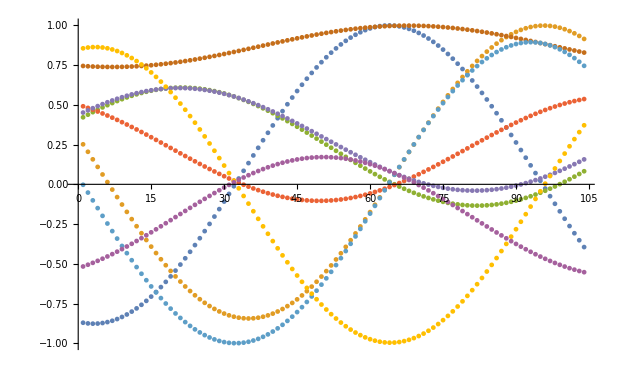

```mathematica
ListPlot[Transpose[Flatten /@ θHistory]]
```

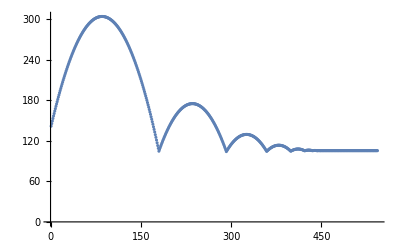

```mathematica
{frame, ball, inputs, car} = ImportPhysicsTickJSONEpisode["dropshot_episode2.json"];
ListPlot[#["location"][[3]] & /@ ball]
```

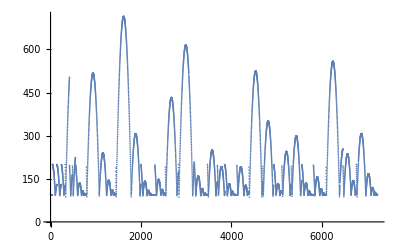

```mathematica
{frame, ball, inputs, car} = ImportPhysicsTickJSONEpisode["soccar_bounces.json"];
ListPlot[#["location"][[3]] & /@ ball]
```

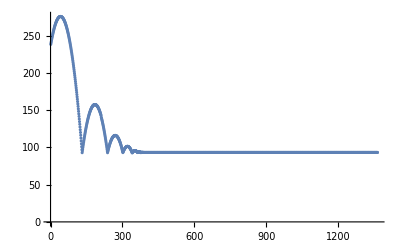

```mathematica
{frame, ball, inputs, car} = ImportPhysicsTickJSONEpisode["soccar_episode.json"];
ListPlot[#["location"][[3]] & /@ ball, PlotRange->All]
```

```mathematica
range = 150;;-1;
```

```mathematica
range = 1;;-1;
```

```mathematica
car = car[[range]];
frame = frame[[range]] - frame[[range[[1]]]];
ball=ball[[range]];
inputs=inputs[[range]];
```

```mathematica
time = frame /120.0;
pos = #["location"] & /@ ball;
vel = #["velocity"] & /@ ball;
angvel = #["angular_velocity"] & /@ ball;
```

```mathematica
a = Quiet[(vel[[2;;-1]] - vel[[1;;-2]])/(t[[2;;-1]] - t[[1;;-2]])];
```

```mathematica
drag = # + {0, 0, 650.0} & /@ a;
```

```mathematica
drag/vel[[1;;-2]];
```

```mathematica
MBall = 30.0;
g = -650.0;
Δt = 1.0/120.0;
CR = 0.6;
c = -0.03144;
Y = 2.0;
μ = 0.286;
ωMax = 6.0;
```

```mathematica
(* soccar and hoops *)
RBall = 93.15;
RBounce = 91.25;
IBall = 2/5 MBall RBounce^2
```

99918.8

```mathematica
(* dropshot *)
RBall = 103.6;
RBounce = 100.45;
IBall = 2/5 MBall RBall^2
```

128796.

```mathematica
.0305 * 30
```

0.915

```mathematica
Round
```

```mathematica
bounce[x_, v_, ω_, n_] := Module[{p, MReduced,vPerp, vPara, ratio, vNext, ωNext, jPerp, jPara, J},
p= x * {1, 1, 0};
MReduced = 1.0/(1/MBall+ ((p-x).(p-x))/IBall);

vPerp = Min[(v.n), 0] n;
vPara = v - vPerp - Cross[p-x, ω];

jPerp = -(1+CR) MBall vPerp;
jPara = -Min[1, 2.0 Norm[vPerp]/Norm[vPara]] MReduced vPara;

J = jPerp + jPara;

vNext = v + J/MBall;
ωNext = ω + Cross[p-x, J]/IBall;

ωNext *=Min[1,ωMax/Norm[ωNext]];

{vNext, ωNext}
]

simulate[x0_, v0_, ω0_, numSteps_] := Module[{t, x, v,Δv, a, vUncorrected, ω, tContact, F},
x = ConstantArray[0, {numSteps, 3}];
v = ConstantArray[0, {numSteps, 3}];
ω = ConstantArray[0, {numSteps, 3}];
t = Table[(i-1)Δt, {i, 1, numSteps}];

x[[1]]=x0;
v[[1]]=v0;
ω[[1]]=ω0;

Do[
If[x[[i-1, 3]]<RBall,
{v[[i]], ω[[i]]} = bounce[x[[i-1]],v[[i-1]], ω[[i-1]], {0,0,1}];
x[[i]] = x[[i-1]]+v[[i]]Δt;
x[[i,3]] = Max[x[[i,3]], 1.0001 RBall];
a =c*v[[i]];
v[[i]] = v[[i]] +a Δt;
,
a = {0,0,g} + c*v[[i-1]];
v[[i]] = v[[i-1]] +a Δt;
ω[[i]] = ω[[i-1]];
x[[i]] = x[[i-1]] +v[[i]] Δt;
];
,
{i, 2, numSteps}
];
{t, x, v, ω}
]
```

```mathematica
Transpose[{pos[[ids,3]], vel[[ids,3]],x[[ids, 3]], v[[ids,3]]}] // MatrixForm
```

(94.31 | -40.661 | 95.0894 | -29.8235
93.93 | -46.061 | 94.7958 | -35.2324
93.5 | -51.461 | 94.4571 | -40.6398
93.03 | -56.861 | 94.0734 | -46.0458
93.31 | 34.101 | 93.6446 | -51.4504
93.55 | 28.671 | 93.1708 | -56.8536
93.74 | 23.241 | 92.6521 | -62.2554
93.89 | 17.811 | 93.1593 | 37.3435
93.99 | 12.381 | 93.4253 | 31.917
94.05 | 6.961 | 93.6461 | 26.492
94.06 | 1.541 | 93.8216 | 21.0684
94.03 | -3.871 | 93.952 | 15.6462
93.95 | -9.281 | 94.0372 | 10.2254
93.83 | -14.691 | 94.0773 | 4.80607
93.66 | -20.101 | 94.0722 | -0.611858
93.45 | -25.511 | 94.0219 | -6.02836
93.19 | -30.921 | 93.9266 | -11.4435
92.89 | -36.321 | 93.7861 | -16.8571
93.07 | 21.781 | 93.6005 | -22.2694
93.21 | 16.351 | 93.3699 | -27.6802
93.3 | 10.931 | 93.0941 | -33.0896
93.35 | 5.511 | 93.2596 | 19.8486
93.35 | 0.091 | 93.3798 | 14.4267
93.31 | -5.321 | 93.4548 | 9.00625
93.22 | -10.731 | 93.4847 | 3.58723
93.09 | -16.141 | 93.4695 | -1.83038
93.17 | 9.681 | 93.4091 | -7.24656
93.21 | 4.261 | 93.3036 | -12.6613
93.2 | -1.151 | 93.1529 | -18.0747
93.15 | -6.561 | 92.9572 | -23.4866
93.18 | 3.931 | 93.1593 | 14.0883
93.17 | -1.481 | 93.2315 | 8.66792
93.11 | -6.891 | 93.2586 | 3.24898
93.14 | 4.131 | 93.2406 | -2.16854
93.14 | 0. | 93.1773 | -7.58464
93.14 | 0. | 93.069 | -12.9993
93.14 | 0. | 93.1593 | 7.79755
93.14 | 0. | 93.1791 | 2.37884
93.14 | 0. | 93.1538 | -3.03845
93.14 | 0. | 93.0834 | -8.45432
93.14 | 0. | 93.1593 | 5.07127
93.14 | 0. | 93.1564 | -0.34673
93.14 | 0. | 93.1084 | -5.76331
93.14 | 0. | 93.1593 | 3.45708
93.14 | 0. | 93.143 | -1.9605
93.14 | 0. | 93.1593 | 1.17599
93.14 | 0. | 93.124 | -4.24099
93.14 | 0. | 93.1593 | 2.54392
93.14 | 0. | 93.1354 | -2.87341
93.14 | 0. | 93.1593 | 1.72359
93.14 | 0. | 93.1285 | -3.69352
93.14 | 0. | 93.1593 | 2.21553
93.14 | 0. | 93.1326 | -3.20171
93.14 | 0. | 93.1593 | 1.92052
93.14 | 0. | 93.1302 | -3.49665
93.14 | 0. | 93.1593 | 2.09744
93.14 | 0. | 93.1317 | -3.31978
93.14 | 0. | 93.1593 | 1.99135
93.14 | 0. | 93.1308 | -3.42584
93.14 | 0. | 93.1593 | 2.05497
93.14 | 0. | 93.1313 | -3.36224
93.14 | 0. | 93.1593 | 2.01681
93.14 | 0. | 93.131 | -3.40038
93.14 | 0. | 93.1593 | 2.03969
93.14 | 0. | 93.1312 | -3.37751
93.14 | 0. | 93.1593 | 2.02597
93.14 | 0. | 93.1311 | -3.39122
93.14 | 0. | 93.1593 | 2.0342
93.14 | 0. | 93.1311 | -3.383
93.14 | 0. | 93.1593 | 2.02927
93.14 | 0. | 93.1311 | -3.38793
93.14 | 0. | 93.1593 | 2.03223
93.14 | 0. | 93.1311 | -3.38497
93.14 | 0. | 93.1593 | 2.03045
93.14 | 0. | 93.1311 | -3.38675
93.14 | 0. | 93.1593 | 2.03152
93.14 | 0. | 93.1311 | -3.38568
93.14 | 0. | 93.1593 | 2.03088
93.14 | 0. | 93.1311 | -3.38632
93.14 | 0. | 93.1593 | 2.03126
93.14 | 0. | 93.1311 | -3.38594
93.14 | 0. | 93.1593 | 2.03103
93.14 | 0. | 93.1311 | -3.38617
93.14 | 0. | 93.1593 | 2.03117
93.14 | 0. | 93.1311 | -3.38603
93.14 | 0. | 93.1593 | 2.03109
93.14 | 0. | 93.1311 | -3.38611
93.14 | 0. | 93.1593 | 2.03114
93.14 | 0. | 93.1311 | -3.38606
93.14 | 0. | 93.1593 | 2.03111
93.14 | 0. | 93.1311 | -3.38609
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03111
93.14 | 0. | 93.1311 | -3.38609
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608
93.14 | 0. | 93.1593 | 2.03112
93.14 | 0. | 93.1311 | -3.38608)

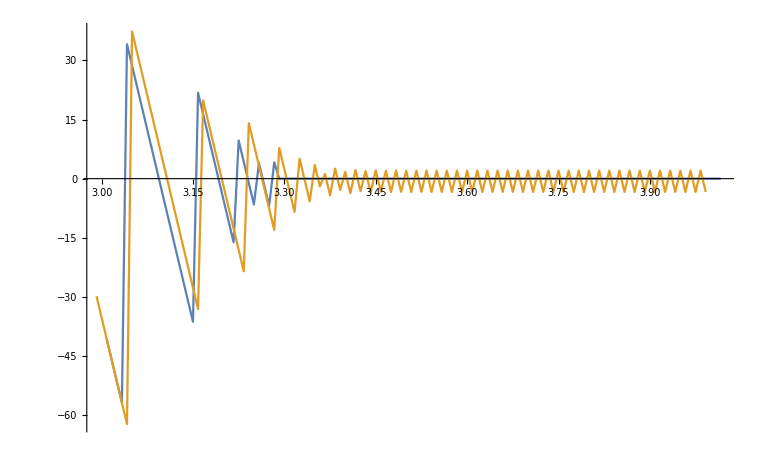

```mathematica
{t, x, v, w} = simulate[pos[[1]], vel[[1]], angvel[[1]],Length[pos]];
ids =360;;480;
ListLinePlot[{
Transpose[{time[[ids]], vel[[ids,3]]}],
Transpose[{t[[ids]], v[[ids,3]]}]
}, PlotRange->All]
```

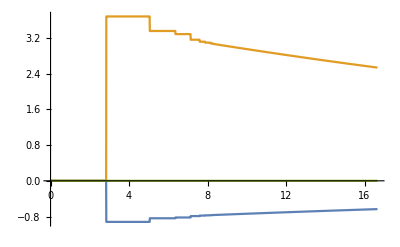

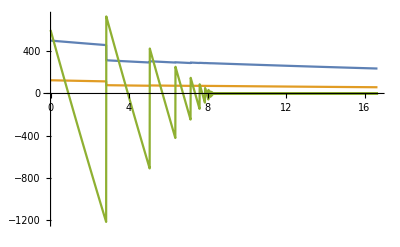

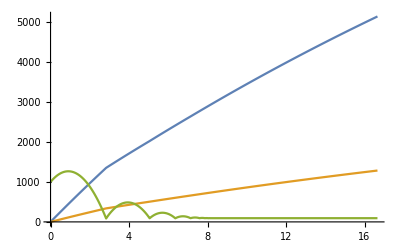

```mathematica
{t, x, v, w} = simulate[{0.0, 0.0, 1000.0}, {500.0,125.0, 600.0}, {0.0, 0.0, 0.0},2000];
ListLinePlot[{
Transpose[{t, w[[All,1]]}],
Transpose[{t, w[[All,2]]}],
Transpose[{t, w[[All,3]]}]
}, PlotRange->All]

ListLinePlot[{
Transpose[{t, v[[All,1]]}],
Transpose[{t, v[[All,2]]}],
Transpose[{t, v[[All,3]]}]
}, PlotRange->All]

ListLinePlot[{
Transpose[{t, x[[All,1]]}],
Transpose[{t, x[[All,2]]}],
Transpose[{t, x[[All,3]]}]
}, PlotRange->All]
```

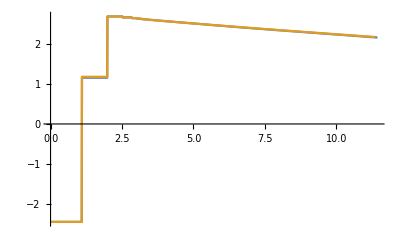

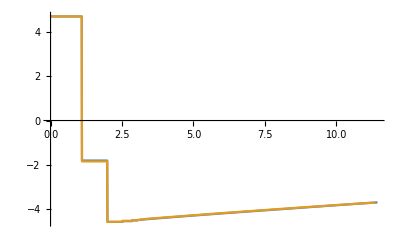

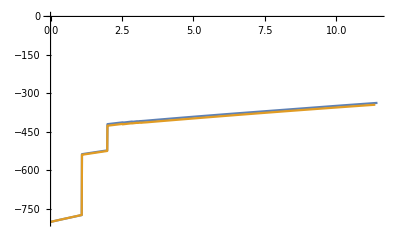

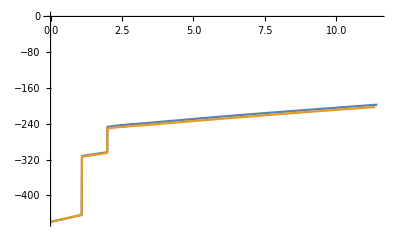

```mathematica
{t, x, v, w} = simulate[pos[[1]], vel[[1]], angvel[[1]],Length[pos]];
ListLinePlot[{
Transpose[{time, angvel[[All,1]]}],
Transpose[{t, w[[All,1]]}]
}, PlotRange->All]

ListLinePlot[{
Transpose[{time, angvel[[All,2]]}],
Transpose[{t, w[[All,2]]}]
}, PlotRange->All]

ListLinePlot[{
Transpose[{time, vel[[All,1]]}],
Transpose[{t, v[[All,1]]}]
}, PlotRange->All]

ListLinePlot[{
Transpose[{time, vel[[All,2]]}],
Transpose[{t, v[[All,2]]}]
}, PlotRange->All]
```

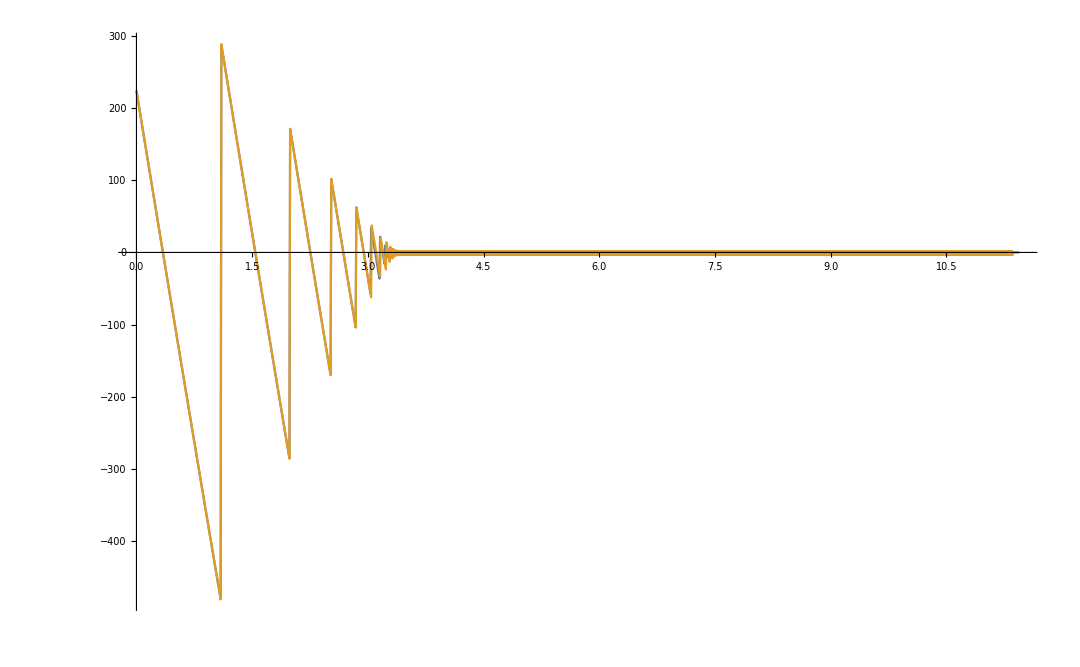

```mathematica
ListLinePlot[{
Transpose[{time, vel[[All,3]]}],
Transpose[{t, v[[All,3]]}]
}, PlotRange->All]
```

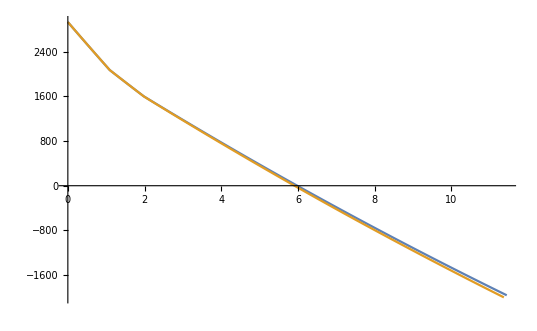

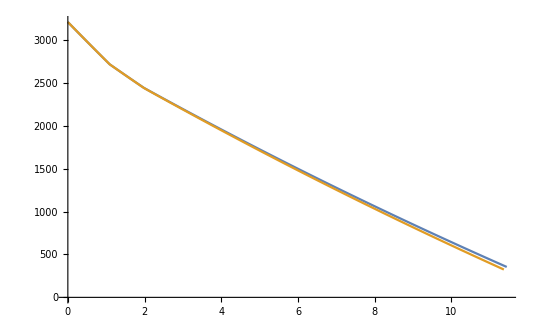

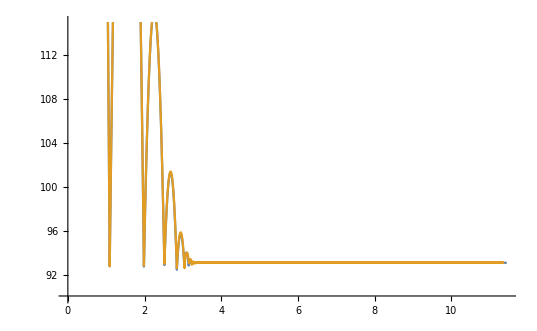

```mathematica
ListLinePlot[{
Transpose[{time, pos[[All,1]]}],
Transpose[{t, x[[All,1]]}]
}]
ListLinePlot[{
Transpose[{time, pos[[All,2]]}],
Transpose[{t, x[[All,2]]}]
}]
ListLinePlot[{
Transpose[{time, pos[[All,3]]}],
Transpose[{t, x[[All,3]]}]
}, PlotRange->{90, 115}]
```

```mathematica
bounces = {};
Do[
If[pos[[i, 3]] < 120 && vel[[i, 3]] < 0 && vel[[i+1,3]] > 0 && Abs[vel[[i+1,3]]]/Abs[vel[[i,3]]]< 0.9,
AppendTo[bounces,i]
]
,
{i, 1, Length[vel]-1}
]
bounces
```

{132,238,302,341,363,377,385,389,392}

```mathematica
105.6
```

```mathematica
Min[xbefore[[All, 3]]]
```

105.599

```mathematica
xbefore = Table[pos[[i]]-vel[[i]]/120.0, {i, bounces}];
before = Table[{pos[[i]], vel[[i]], angvel[[i]]}, {i, bounces}];
after = Table[{vel[[i+1]], angvel[[i+1]]}, {i, bounces}];
```

```mathematica
after[[All,1, 3]]/before[[All,2, 3]]
```

{-0.599834,-0.59984,-0.599838,-0.599773,-0.599726,-0.599681,-0.599777,-0.599146,-0.599478}

```mathematica
bounce2[{x_, v_, ω_}] := Module[
{n = {0, 0, 1},p,vPerp, vPara, vNext, ωNext, jPerp, jPara, J},
p= x * {1, 1, 0};
MReduced = 1.0/(1/MBall+ ((p-x).(p-x))/IBall);

vPerp = (v.n) n;
vPara = (v - vPerp) - Cross[p-x, ω];

jPerp = -(1+CR) MBall vPerp;
jPara = -Min[1, 2.0 Norm[vPerp]/Norm[vPara]] MReduced vPara;

J = jPerp + jPara;

vNext = v + J/MBall;
ωNext = ω + Cross[p-x, J]/IBall;

ωNext *=Min[1,ωMax/Norm[ωNext]];

{vNext, ωNext}
]
```

```mathematica
Median[Flatten[Abs[((Flatten[bounce2[#]] & /@ before) - Flatten /@ after)/(Flatten /@ after)]]]
```

0.00543614

```mathematica
Median[Flatten[Abs[((Flatten[bounce2[#]] & /@ before) - Flatten /@ after)/(Flatten /@ after)]]]
```

0.00162981

```mathematica
NMinimize[Norm[Flatten[((Flatten[bounce2[#, {a0,a1}]] & /@ before) - Flatten /@ after)/(Flatten /@ after)]], {a0, a1}]
```

{0.109412,{a0→100.238,a1→0.283738}}

```mathematica
D[Cross[{a1, a2, a3}, {b1, b2, b3}],{{b1, b2, b3}}] // MatrixForm
```

(0 | -a3 | a2
a3 | 0 | -a1
-a2 | a1 | 0)

```mathematica
L = ({{0, -a3, a2}, {a3, 0, -a1}, {-a2, a1, 0}});
```

```mathematica
d = DiagonalMatrix[{d1, d2, d3}]
```

{{d1,0,0},{0,d2,0},{0,0,d3}}

```mathematica
L.d.L
```

{{-a3^2 d2-a2^2 d3,a1 a2 d3,a1 a3 d2},{a1 a2 d3,-a3^2 d1-a1^2 d3,a2 a3 d1},{a1 a3 d2,a2 a3 d1,-a2^2 d1-a1^2 d2}}